# Hypersingular Euler-Maclaurin expansion

Here we analyse the error of the HSEM expansion up to a certain finite order.

```mathematica
$MinPrecision=15;
```

## Parameter Choices

Order of the SEM operator and value of ν. For numerical reasons, choose ν∈ C∖N, where ν can be arbitrarily close to any integer number.

```mathematica
semOperatorOrder=12;
νFixed=2+1/1000;
```

## Lattice Sums

using the results from McPhedran et al (2003)

```mathematica
pUpper=30;
```

Lattice Sum:x1^(2n)/((x1^2+x2^2)^(p+n)), double sum offers exponential convergence. Only works for n>0!

```mathematica
LatticeSumPart[n_,s_]=2*Sqrt[Pi]*Gamma[s+n-1/2]*Zeta[2s-1]/Gamma[s+n]+8*Pi^s/Gamma[s+n]Sum[(p2/p1)^(s-1/2)*p1^n*p2^n*Pi^n*BesselK[s+n-1/2,2Pi*p1*p2],{p1,1,pUpper},{p2,1,pUpper}];
```

Lattice Sum:SolidHarmonic[{x1,x2},k]/((x1^2+x2^2)^(ν/2))=(x1^k+...)/((x1^2+x2^2)^(ν/2)), only nonzero for k a multiple of 4 due to symmetries of the square lattice.

```mathematica
GenerateLatticeSumAng[l_]:=If[Mod[l,4]==0,(((ChebyshevT[l,x]-1)/.{x^n_->LatticeSumPart[n/2,s]})+2LatticeSumPart[1,s])/.{s->(ν-l)/2},0]
```

where the last term generates the n = 0 contribution (which is excluded by the -1 in brackets, as above formula holds for n>0 only).

Evaluate the lattice sum for a solid harmonic of degree l.

```mathematica
ComputeLatticeSum[ν0_,l_]:=N[Evaluate[GenerateLatticeSumAng[l]]/.{ν->ν0},30];
```

```mathematica
ComputeLatticeSum[1/2,16]
```

72073.3410944692046107985171373

## Solid Harmonics

```mathematica
GenerateSolidHarmonic2D[k_]:=Cos[k*ϕ]*Sqrt[(x1^2+x2^2)]^k/.{ϕ->ArcTan[x1/x2]}//TrigExpand//FullSimplify;
```

Generate a differential operator out of the solid harmonics.

```mathematica
SolidDiffOp[k_]:=(GenerateSolidHarmonic2D[k]/.{x1^n1_ x2^_n2 ->DiffOp[n1,n2]})/.{x1^n1_->DiffOp[n1,0],x2^n2_->DiffOp[0,n2]};
```

Generate a differential operator out of the symbol of the poly-Laplacian.

```mathematica
PolyLaplaceDiffOp[k_]:=If[k==0,DiffOp[0,0],(If[Mod[k,2]==0,(Expand[Sqrt[(x1^2+x2^2)]^k]),0]/.{x1^n1_ x2^n2_ ->DiffOp[n1,n2]})/.{x1^n1_->DiffOp[n1,0],x2^n2_->DiffOp[0,n2]},0];
```

Differential Operator, generated from products of poly-Laplacians and solid harmonic differential operators.

```mathematica
LaplaceSolidDiffOp[kRadial_,kAngular_]:=((If[Mod[kRadial,2]==0&&Mod[kAngular,2]==0,(x1^2+x2^2)^(kRadial/2)*GenerateSolidHarmonic2D[kAngular],0]//Expand)/.{x1^n1_ x2^n2_ ->DiffOp[n1,n2]})/.{x1^n1_->DiffOp[n1,0],x2^n2_->DiffOp[0,n2]}
```

## Spherical Expansion

Expansion of (z · (∇))^k into solid harmonics

Spherical Expansion of the SEM Differential operator

```mathematica
SphericalExpansionDiffOp[k_]:=If[Mod[k,2]==0,1/(2Pi)Integrate[Cos[ϕ]^(k),{ϕ,0,2Pi}]AngLatSum[ν-k,0]PolyLaplaceDiffOp[k]+Sum[1/Pi*Integrate[Cos[ϕ]^(k)*Cos[2n*ϕ],{ϕ,0,2Pi}]*(AngLatSum[ν-k+2n,2n]*LaplaceSolidDiffOp[k-2n,2n]),{n,1,k/2}],0]
```

Symbolic SEM Differential Operator. Collect Lattice Sums, such that if evaluated, they need only be computed once.

```mathematica
DiffOp[l_]:=Collect[If[Mod[l,2]==0,Sum[1/(2k)!*SphericalExpansionDiffOp[2k]//Expand,{k,0,l/2}],0],AngLatSum[_,_],Together];
```

## SEM Operator

Generator for the SEM Differential Operator up to derivatives of order l. Lattice sums are now evaluated, so this takes some time.

```mathematica
GenerateDiffOp[ν1_,l_]:=(DiffOp[l]/.{ν->ν1})/.AngLatSum->ComputeLatticeSum;
```

```mathematica
SEMOp=GenerateDiffOp[νFixed,semOperatorOrder];
```

# Test Summation and Integration

## Test Function

2D Test Function: We choose gaussian function with width proportional to 1/σ1.

```mathematica
TestFunc2DExp[x1_,x2_,σ1_]=Exp[-(x1^2+x2^2)*σ1^2];
```

```mathematica
SEMOpEvaluatedExp[x1_,x2_,σ1_]=(SEMOp/.{DiffOp[n1_,n2_]:>D[TestFunc2DExp[x1,x2,σ1],{x1,n1},{x2,n2}]});
```

## Integral

Integral ∫s(z-x)g(z)ⅆz, evaluated in Fourier space by using the convolution theorem

```mathematica
$Assumptions={σ1>0,ν>0,x1∈Reals,x2∈Reals}
```

{σ1>0,ν>0,x1∈ℝ,x2∈ℝ}

```mathematica
IntFuncExp[x1_,x2_,ν_,σ1_]=(π^(-1+ν) Gamma[1-ν/2])/Gamma[ν/2] Integrate[k*2 π BesselJ[0,2 π k √(x1^2+x2^2)]*k^(ν-2)*(ⅇ^(-(k^2* π^2)/σ1^2) π)/σ1^2,{k,0,Infinity}]//Normal
```

π σ1^(-2+ν) Gamma[1-ν/2] LaguerreL[-ν/2,-(x1^2+x2^2) σ1^2]

## Sum

Sum ∑' s(z-x) g(z)

```mathematica
sumUpper=150;
```

```mathematica
SumValueExp[x1_,x2_,σ1_]=N[Sum[If[Norm[{y1,y2}]≠0,1/Sqrt[y1^2+y2^2]^νFixed*Func[y1-x1,y2-x2,σ1],0],{y1,-sumUpper,sumUpper},{y2,-sumUpper,sumUpper}]/.{Func->TestFunc2DExp},25];
```

## Absolute SEM Error

SEM absolute error with  σ=1/λ.

```mathematica
SEMAbsoluteErrorExp[x1_,x2_,σ1_]:=Module[{sumValue,errorValue},
sumValue=SumValueExp[x1,x2,σ1];
errorValue=Abs[(N[sumValue-IntFuncExp[x1,x2,νFixed,σ1]-SEMOpEvaluatedExp[x1,x2,σ1],25])];
Return[errorValue]]
```

```mathematica
GenerateValueTab[λ_]:=ParallelTable[If[x1>=x2,SumValueExp[x1,x2,1/λ],0],{x1,0,5*λ,1},{x2,0,5*λ,1}];
```

```mathematica
GenerateIntegralTab[λ_]:=ParallelTable[If[x1>=x2,N[IntFuncExp[x1,x2,νFixed,1/λ],30],0],{x1,0,5*λ,1},{x2,0,5*λ,1}];
```

```mathematica
For[i=0,i≤6,i++,SEMOperatorEvaluatedExp[x1_,x2_,σ1_,2i]=(GenerateDiffOp[νFixed,2i]/.{DiffOp[n1_,n2_]:>D[TestFunc2DExp[x1,x2,σ1],{x1,n1},{x2,n2}]});]
```

```mathematica
GenerateSEMOperatorTab[λ_,i_]:=ParallelTable[If[x1>=x2,N[SEMOperatorEvaluatedExp[x1,x2,1/λ,2i],30],0],{x1,0,5*λ,1},{x2,0,5*λ,1}];
```

```mathematica
valueTab=Table[GenerateValueTab[λ],{λ,1,10}];
```

```mathematica
integralTab=Table[GenerateIntegralTab[λ],{λ,1,10}];
```

```mathematica
SEMOperatorTabTab=Table[Table[GenerateSEMOperatorTab[λ,i],{λ,1,10}],{i,0,6}];
```

```mathematica
maxErrorAbsolute0=Table[{i,Max[Max[Abs[valueTab[[i]]-integralTab[[i]]-SEMOperatorTabTab[[0/2+1]][[i]]]]]},{i,1,10}];
```

```mathematica
maxErrorAbsolute2=Table[{i,Max[Max[Abs[valueTab[[i]]-integralTab[[i]]-SEMOperatorTabTab[[2/2+1]][[i]]]]]},{i,1,10}];
```

```mathematica
maxErrorAbsolute4=Table[{i,Max[Max[Abs[valueTab[[i]]-integralTab[[i]]-SEMOperatorTabTab[[4/2+1]][[i]]]]]},{i,1,10}];
```

```mathematica
maxErrorAbsolute8=Table[{i,Max[Max[Abs[valueTab[[i]]-integralTab[[i]]-SEMOperatorTabTab[[8/2+1]][[i]]]]]},{i,1,10}];
```

```mathematica
maxErrorAbsolute10=Table[{i,Max[Max[Abs[valueTab[[i]]-integralTab[[i]]-SEMOperatorTabTab[[10/2+1]][[i]]]]]},{i,1,10}];
```

```mathematica
maxErrorAbsolute12=Table[{i,Max[Max[Abs[valueTab[[i]]-integralTab[[i]]-SEMOperatorTabTab[[6+1]][[i]]]]]},{i,1,10}];
```

Maximum absolute error as a function of λ

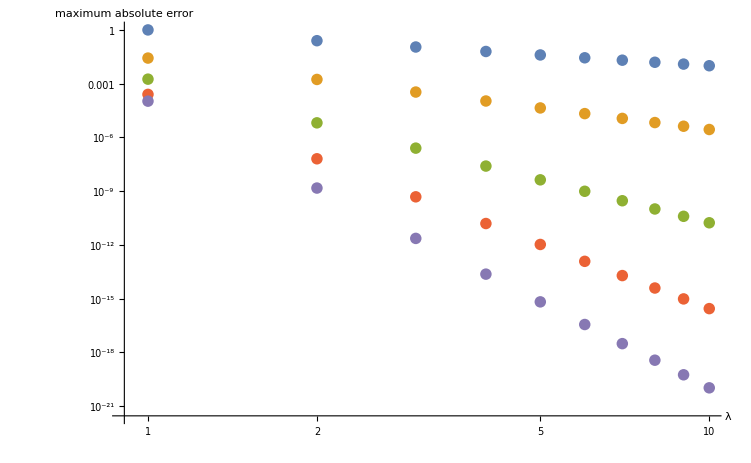

```mathematica
ListLogLogPlot[{maxErrorAbsolute0,maxErrorAbsolute2,maxErrorAbsolute4,maxErrorAbsolute8,maxErrorAbsolute12},AxesLabel->{"λ","maximum absolute error"}]
```

# Plots for different interaction exponents

ν = 1: Coulomb interaction

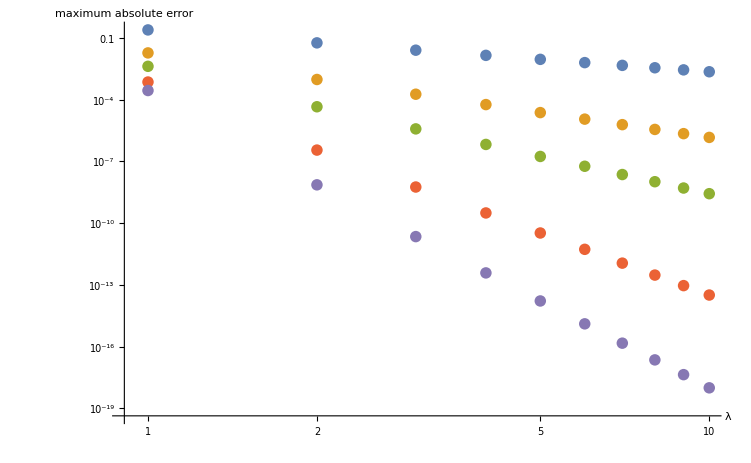
```mathematica
plotNu1=-Graphics-;
```

ν = 2: inverse square interaction

```mathematica
plotNu2=-Graphics-;
```

ν = 3: dipole interaction

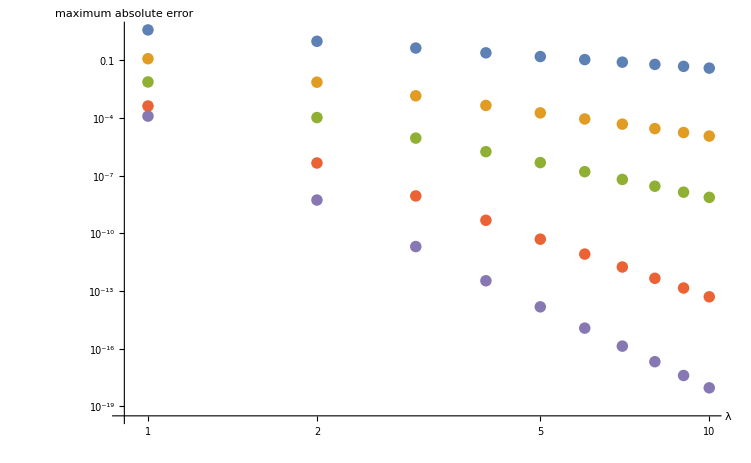
```mathematica
plotNu3=-Graphics-;
```